# Cuestionario_05: Integral Aproximada.

1.      	a) Obtén la integral aproximada de ∫_0^1 Cos[x]/(x+1)ⅆx usando la regla de los trapecios con n=10.
            b) Calcula la segunda derivada de  f(x)= Cos[x]/(x+1) y usando la gráfica que consideres oportuna encuentra un valor para M2 (fórmula de los trapecios).  Utiliza ese valor de para acotar el error cometido en la aproximación del apartado anterior y calcula el número de dígitos exactos que tienes en la aproximación del apartado anterior.

```mathematica
NIntegrate[Cos[x]/(x+1),{x,0,1}]
```

0.601044

```mathematica
D[Cos[x]/(x+1),{x,2}]
```

(2 Cos[x])/(1+x)^3-Cos[x]/(1+x)+(2 Sin[x])/(1+x)^2

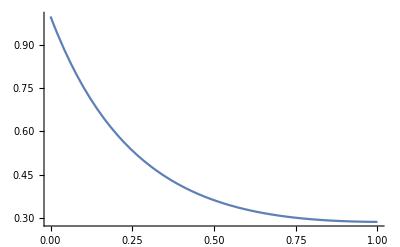

```mathematica
Plot[Abs[(2 Cos[x])/(1+x)^3-Cos[x]/(1+x)+(2 Sin[x])/(1+x)^2],{x,1,0}]
```

```mathematica
f[x_]:=Cos[x]/(x+1)
```

```mathematica
Trapezoid[a_,b_,n_,d_,f_]:=N[(f[a]+f[b]+2 ∑_(k=1)^(n-1) f[a+k ((b-a)/n)])((b-a)/(2  n)),d]
ErrorTrapezoid[a_,b_,n_,M2_]:= (b-a)^3/(12 n^2)M2;
```

```mathematica
Trapezoid[0,1,10,20,f]
```

0.60141412919716912939

```mathematica
N[%,20]
```

0.60141412919716912939

```mathematica
ErrorTrapezoid[0,1,10,1]
```

1/1200

```mathematica
N[%]
```

0.000833333

El valor aproximado de        ∫_0^1 Cos[x]/(x+1)ⅆx usando la regla de los trapecios con 10 subdivisiones es      ∫_0^1 Cos[x]/(x+1)≈    0.601414129     
             y el valor de M2=        1               y el número de dígitos exactos obtenidos es 2

La aproximación obtenida con Mathematica es (usa NIntegrate)∫_0^1 Cos[x]/(x+1)≈0.601044

2.      	a) Obtén el número de particiones necesario para que usando la regla de Simpson obtengamos la integral aproximada de ∫_0^1 Cos[x]/(x+1)ⅆx con al menos 3 dígitos decimales exactos.
            b) Calcula el valor de la integral usando la regla de Simpson con las particiones que has obtenido en el apartado anterior.

```mathematica
Simpson[a_,b_,n_,d_,f_]:=N[(f[a]+f[b]+4∑_(k=0)^((n/2)-1) f[a+(2  k + 1)((b-a)/n)]+2 ∑_(k=1)^((n/2)-1) f[a+2  k ((b-a)/n) ])((b-a)/(3 n)),d];
ErrorSimpson[a_,b_,n_,M4_]:= (b-a)^5/(180 n^4)M4;
```

```mathematica
f[x_]:=Cos[x]/(x+1)
```

```mathematica
D[Cos[x]/(x+1),{x,4}]
```

(24 Cos[x])/(1+x)^5-(12 Cos[x])/(1+x)^3+Cos[x]/(1+x)+(24 Sin[x])/(1+x)^4-(4 Sin[x])/(1+x)^2

```mathematica
Simplify[(24 Cos[x])/(1+x)^5-(12 Cos[x])/(1+x)^3+Cos[x]/(1+x)+(24 Sin[x])/(1+x)^4-(4 Sin[x])/(1+x)^2]
```

((13-20 x-6 x^2+4 x^3+x^4) Cos[x]-4 (-5-3 x+3 x^2+x^3) Sin[x])/(1+x)^5

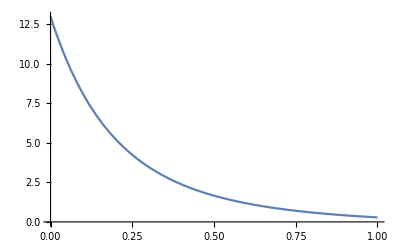

```mathematica
Plot[((13-20 x-6 x^2+4 x^3+x^4) Cos[x]-4 (-5-3 x+3 x^2+x^3) Sin[x])/(1+x)^5,{x,0,1}]
```

```mathematica
((13-20 x-6 x^2+4 x^3+x^4) Cos[x]-4 (-5-3 x+3 x^2+x^3) Sin[x])/(1+x)^5/.x->0
```

13

```mathematica
Reduce[(1)^5/(180 n^4)13≤ 10^-4,n]
```

n≤-√(2/3) 5^(3/4) 13^(1/4)||n≥√(2/3) 5^(3/4) 13^(1/4)

```mathematica
N[%]
```

n≤-5.18403||n≥5.18403

```mathematica
Simpson[0,1,6,20,f]
```

0.60105640102293495314

El número de particiones que necesitamos es n=6 (recordar n par en Simpson)              

El valor aproximado de        ∫_0^1 Cos[x]/(x+1)ⅆx usando la regla de Simpson con n=6 es ∫_0^1 Cos[x]/(x+1)≈0.601

La aproximación obtenida con Mathematica es (usa  NIntegrate)∫_0^1 Cos[x]/(x+1)≈0.601044